```mathematica
NA = 6.0221367 10^23;
Dtot=10^-11;
kf=10^6 / NA;
kd=10^3;
sigma=1 10^-7;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
t=0.01;
```

```mathematica
ciccio=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=ciccio[[1,1,2]];
beta = ciccio[[1,2,2]];
gamma=ciccio[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

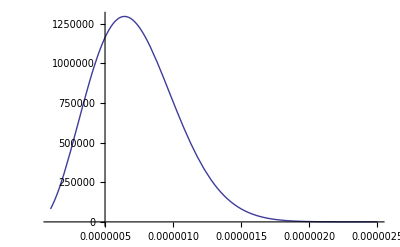

```mathematica
Plot[f[r], {r,sigma,sigma 25}]
```

```mathematica
out=Table[{r,f[r]},{r,sigma,sigma 25,(sigma 25 - sigma) / 100}] // N
```

{{1.×10^-7,81664.3},{1.24×10^-7,124463.},{1.48×10^-7,175026.},{1.72×10^-7,232528.},{1.96×10^-7,296037.},{2.2×10^-7,364534.},{2.44×10^-7,436936.},{2.68×10^-7,512113.},{2.92×10^-7,588911.},{3.16×10^-7,666175.},{3.4×10^-7,742770.},{3.64×10^-7,817597.},{3.88×10^-7,889618.},{4.12×10^-7,957866.},{4.36×10^-7,1.02147×10^6},{4.6×10^-7,1.07964×10^6},{4.84×10^-7,1.13173×10^6},{5.08×10^-7,1.17718×10^6},{5.32×10^-7,1.21557×10^6},{5.56×10^-7,1.2466×10^6},{5.8×10^-7,1.27008×10^6},{6.04×10^-7,1.28596×10^6},{6.28×10^-7,1.29429×10^6},{6.52×10^-7,1.29522×10^6},{6.76×10^-7,1.28903×10^6},{7.×10^-7,1.27605×10^6},{7.24×10^-7,1.25669×10^6},{7.48×10^-7,1.23146×10^6},{7.72×10^-7,1.20087×10^6},{7.96×10^-7,1.1655×10^6},{8.2×10^-7,1.12596×10^6},{8.44×10^-7,1.08285×10^6},{8.68×10^-7,1.0368×10^6},{8.92×10^-7,988408.},{9.16×10^-7,938275.},{9.4×10^-7,886968.},{9.64×10^-7,835026.},{9.88×10^-7,782949.},{1.012×10^-6,731197.},{1.036×10^-6,680184.},{1.06×10^-6,630278.},{1.084×10^-6,581797.},{1.108×10^-6,535012.},{1.132×10^-6,490148.},{1.156×10^-6,447382.},{1.18×10^-6,406849.},{1.204×10^-6,368643.},{1.228×10^-6,332821.},{1.252×10^-6,299407.},{1.276×10^-6,268392.},{1.3×10^-6,239743.},{1.324×10^-6,213405.},{1.348×10^-6,189300.},{1.372×10^-6,167340.},{1.396×10^-6,147420.},{1.42×10^-6,129428.},{1.444×10^-6,113248.},{1.468×10^-6,98756.5},{1.492×10^-6,85830.6},{1.516×10^-6,74347.7},{1.54×10^-6,64187.2},{1.564×10^-6,55232.},{1.588×10^-6,47369.8},{1.612×10^-6,40493.5},{1.636×10^-6,34502.4},{1.66×10^-6,29302.},{1.684×10^-6,24804.7},{1.708×10^-6,20929.9},{1.732×10^-6,17603.5},{1.756×10^-6,14758.2},{1.78×10^-6,12333.2},{1.804×10^-6,10273.8},{1.828×10^-6,8531.02},{1.852×10^-6,7061.4},{1.876×10^-6,5826.44},{1.9×10^-6,4792.29},{1.924×10^-6,3929.27},{1.948×10^-6,3211.54},{1.972×10^-6,2616.69},{1.996×10^-6,2125.34},{2.02×10^-6,1720.87},{2.044×10^-6,1389.03},{2.068×10^-6,1117.69},{2.092×10^-6,896.564},{2.116×10^-6,716.958},{2.14×10^-6,571.558},{2.164×10^-6,454.238},{2.188×10^-6,359.886},{2.212×10^-6,284.255},{2.236×10^-6,223.828},{2.26×10^-6,175.705},{2.284×10^-6,137.506},{2.308×10^-6,107.283},{2.332×10^-6,83.4462},{2.356×10^-6,64.7077},{2.38×10^-6,50.0241},{2.404×10^-6,38.5547},{2.428×10^-6,29.6247},{2.452×10^-6,22.6938},{2.476×10^-6,17.3317},{2.5×10^-6,13.1965}}

```mathematica
Export["p_rev.tsv",out]
```

p_rev.tsv